## Solution CP5: Complex numbers and matrices

This exercise demonstrates how Mathematica can be used to perform calculations with complex numbers, vectors and matrces.

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

## Complex numbers and functions

Notice that when dealing with complex numbers in Mathematica, √-1 is not denoted by i (as is standard in mathematics) but by the capital letter I, as it is standard to use capital letters for special numbers. Mathematica includes a number of commands to perform calculations with complex numbers, such as Re[] and Im[], that return respectively the real and imaginary part of a complex number. The commands Abs[] and Arg[] return the modulus and the argument, and the command AbsArg[] will convert a complex number z into polar coordinates (ω,ϕ) where ω is the radius Abs[z] and ϕ is the angle Arg[z] in the polar notation z=ω·(cos(ϕ)+sin(ϕ)·i). The command Conjugate[] calculates the complex conjugate. 
The commands ListPlot[] and ParametricPlot[] can be used to plot complex numbers and complex-valued functions, respectively. However, for all plotting purposes you need to enter the real and imaginary parts of complex numbers as separate variables. For examples, see chapter 7 of the Mathematica tutorial.

### Exercise 5-1

#### Complex numbers

Consider the following complex numbers: λ_1=1+i, λ_2= -2+1/2 i, λ_3= 1/2-2i.

(a) Plot λ_1, λ_2 and λ_3 in one graph

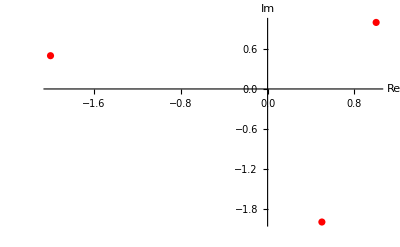

```mathematica
λ1=1+I;
λ2=-2+(1/2)*I;
λ3=(1/2)-2 *I;
λ={λ1,λ2,λ3};
ListPlot[Table[{Re[λ[[k]]],Im[λ[[k]]]},{k,1,3}],PlotStyle->Red, AxesLabel->{"Re","Im"}]
```

(b) Calculate the complex conjugate of  λ_1, λ_2 and λ_3

```mathematica
Conjugate[λ]
```

{1-ⅈ,-2-ⅈ/2,1/2+2 ⅈ}

(c) Calculate the the absolute value and the argument of λ_1, λ_2 and λ_3

```mathematica
Abs[λ]
```

{√2,(√17)/2,(√17)/2}

```mathematica
Arg[λ]
```

{π/4,π-ArcTan[1/4],-ArcTan[4]}

(d) Convert  λ_1, λ_2 and λ_3 into polar coordinates

```mathematica
polar=AbsArg[λ]
p1=polar[[1]];
p2=polar[[2]];
p3=polar[[3]];
```

{{√2,π/4},{(√17)/2,π-ArcTan[1/4]},{(√17)/2,-ArcTan[4]}}

(e) Calculate  3λ_1, 2 λ_2 and -2 λ_3 using both the regular notation and the polar coordinates notation

```mathematica
3*λ1
3*p1
```

3+3 ⅈ

{3 √2,(3 π)/4}

```mathematica
2*λ2
2*p2
```

-4+ⅈ

{√17,2 (π-ArcTan[1/4])}

```mathematica
-2*λ3
-2*p3
```

-1+4 ⅈ

{-√17,2 ArcTan[4]}

(f) Calculate λ_1+λ_3, 2 λ_1+λ_2 and 4 λ_2+λ_3

```mathematica
λ1+λ3
p1+p3
```

3/2-ⅈ

{√2+(√17)/2,π/4-ArcTan[4]}

```mathematica
2*λ1+λ2
2*p1+p2
```

(5 ⅈ)/2

{2 √2+(√17)/2,(3 π)/2-ArcTan[1/4]}

```mathematica
4*λ2+λ3
4*p2+p3
```

-15/2

{(5 √17)/2,4 (π-ArcTan[1/4])-ArcTan[4]}

(g) Calculate λ_1·λ_2, λ_1·λ_3 and λ_2·λ_3 using either the regular notation or the polar coordinates notation

```mathematica
λ1*λ2
p1*p2
```

-5/2-(3 ⅈ)/2

{√(17/2),1/4 π (π-ArcTan[1/4])}

```mathematica
λ1*λ3
p1*p3
```

5/2-(3 ⅈ)/2

{√(17/2),-1/4 π ArcTan[4]}

```mathematica
λ2+λ3
p2*p3
```

-3/2-(3 ⅈ)/2

{17/4,-(π-ArcTan[1/4]) ArcTan[4]}

(h) Calculate  λ_1^4, λ_2^4 and λ_3^4

```mathematica
λ^4
polar^4
```

{-4,161/16-15 ⅈ,161/16+15 ⅈ}

{{4,π^4/256},{289/16,(π-ArcTan[1/4])^4},{289/16,ArcTan[4]^4}}

(i) Calculate 1/λ_1, 1/λ_2 and 1/λ_3

```mathematica
1/λ
1/polar
```

{1/2-ⅈ/2,-8/17-(2 ⅈ)/17,2/17+(8 ⅈ)/17}

{{1/(√2),4/π},{2/(√17),1/(π-ArcTan[1/4])},{2/(√17),-1/ArcTan[4]}}

(j) Calculate λ_1/λ_2, λ_1/λ_3 and λ_2/λ_3 using either the regular notation or the polar coordinates notation

```mathematica
λ1/λ2
p1/p2
```

-6/17-(10 ⅈ)/17

{2 √(2/17),π/(4 (π-ArcTan[1/4]))}

```mathematica
λ1/λ3
p1/p3
```

-6/17+(10 ⅈ)/17

{2 √(2/17),-π/(4 ArcTan[4])}

```mathematica
λ2/λ3
p2/p3
```

-8/17-(15 ⅈ)/17

{1,-(π-ArcTan[1/4])/ArcTan[4]}

(j) Calculate e^iπ , e^(iπ/2) and e^(iπ/4) , and plot them in one graph

{-1,ⅈ,ⅇ^((ⅈ π)/4)}

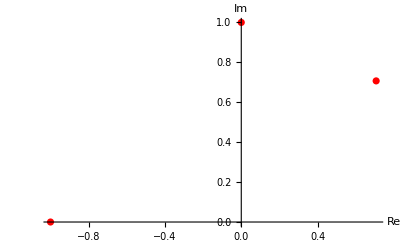

```mathematica
e={Exp[I*Pi],Exp[I*Pi/2],Exp[I*Pi/4]}
ListPlot[Table[{Re[e[[k]]],Im[e[[k]]]},{k,1,3}],PlotStyle->Red, AxesLabel->{"Re","Im"}]
```

#### Complex functions

Consider the function: e^((a+bi)t). Plot this function for the following value pairs (a,b). Hint: implement the function in polar coordinates notation.

(a) a=0.5, b=2π

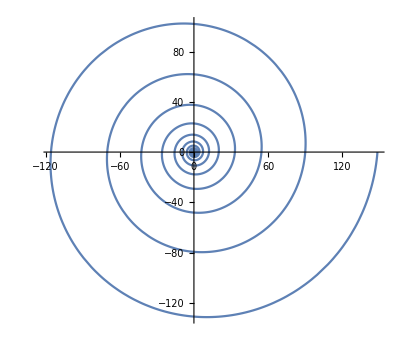

```mathematica
z=a+b*I;
p=Abs[z]*(Cos[Arg[z]]+I*Sin[Arg[z]]);
f=Exp[z*t]/.z->p;
f1=f/.{a->0.5,b->2*Pi};
ParametricPlot[{Re[f1],Im[f1]},{t,0,10},PlotRange->All]
```

Conclusion: the figure spirals outwards (increasing amplitude because of a>0) in a counterclockwise direction (because of b>0)

(b) a=-0.5, b=2π

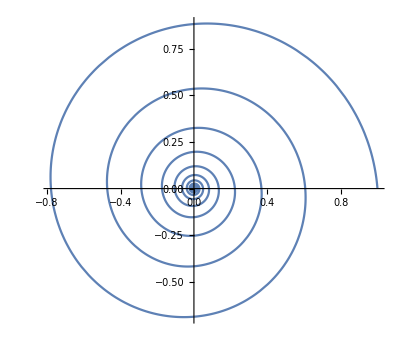

```mathematica
f2=f/.{a->-0.5,b->2*Pi};
ParametricPlot[{Re[f2],Im[f2]},{t,0,10},PlotRange->All]
```

Conclusion: the figure spirals inwards (decreasing amplitude because of a<0) in a counterclockwise direction (because of b>0)

(c) a=0.5, b=-2π

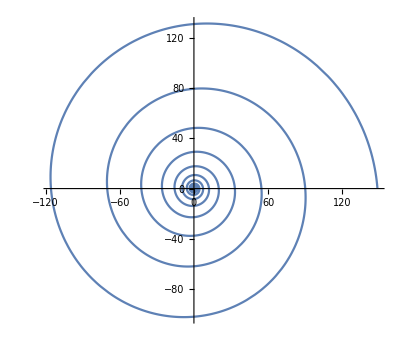

```mathematica
f3=f/.{a->0.5,b->-2*Pi};
ParametricPlot[{Re[f3],Im[f3]},{t,0,10},PlotRange->All]
```

Conclusion: the figure spirals outwards (increasing amplitude because of a>0), but this time in a clockwise fashion (because of b<0).

(d) a=0.1, b=10

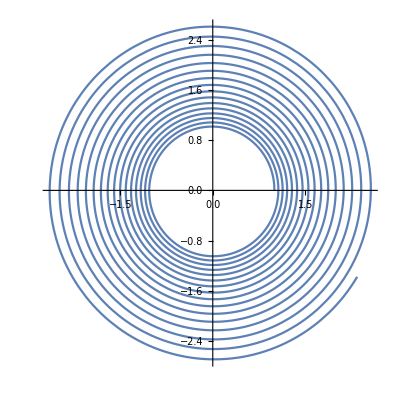

```mathematica
f4=f/.{a->0.1,b->10};
ParametricPlot[{Re[f4],Im[f4]},{t,0,10},PlotRange->All]
```

Conclusion: the figure spirals outwards (increasing amplitude because of a>0) in a counterclockwise direction (because of b>0). The amplitude increases very slowly (since a is rather small) and the speed of rotation is relatively fast (since b is rather large).

## Matrices and vectors

In Mathematica vectors and matrices are represented as lists and nested lists (i.e., a list of lists), respectively. A matrix can be defined using the commands Table[] or Array[]; for examples, see chapter 8 of the Mathematica tutorial. The command MatrixForm[] is used to represent a list as a column vector or as a matrix in matrix notation. Mathematica knows a number of build-in commands to calculate characteristics of a matrix A, such as the trace Tr[A], the determinant Det[A], and the eigenvalues Eigenvalues[A]. The command CharacteristicPolynomial[A,λ] will calculate the characteristic equation of the matrix A for variable λ.

### Exercise 5-2: Multiplying matrices and vectors

Consider the matrices A=(1 | 0
-2 | 1
4 | 3) and B=(2 | 1
1 | -2) from the pen and paper practical.

(a) Calculate the product of A and the first column vector of B

```mathematica
A={{1,0},{-2,1},{4,3}};
B= {{2,1},{1,-2}};
MatrixForm[A]
MatrixForm[B]
```

(1 | 0
-2 | 1
4 | 3)

(2 | 1
1 | -2)

```mathematica
MatrixForm[Dot[A,B[[1]]]]
```

(2
-3
11)

(b) Calculate the product of A and the second column vector of B

```mathematica
MatrixForm[Dot[A,B[[2]]]]
```

(1
-4
-2)

(c) Calculate the matrix product AB

```mathematica
MatrixForm[Dot[A,B]]
```

(2 | 1
-3 | -4
11 | -2)

(d) Calculate the matrix product BA

```mathematica
MatrixForm[Dot[B,A]]
```

Dot::dotsh: Tensors {{2,1},{1,-2}} and {{1,0},{-2,1},{4,3}} have incompatible shapes.

{{2,1},{1,-2}}.{{1,0},{-2,1},{4,3}}

### Exercise 5-3: 2x2 matrices

Consider the matrices A1=(3 | 2
3 | -2), A2=(2 | -3
3 | 2) and A3=(4 | 2
-4 | -2) from the pen and paper practical.

(a) Calculate the sum of A1, A2 and A3

```mathematica
A1=({{3, 2}, {3, -2}});
A2=({{2, -3}, {3, 2}});
A3=({{4, 2}, {-4, -2}});
MatrixForm[A1+A2+A3]
```

(9 | 1
2 | -2)

(b) Calculate the product of A1, A2 and A3

```mathematica
MatrixForm[Dot[A1,A2,A3]]
MatrixForm[A1.A2.A3]
```

(68 | 34
52 | 26)

(68 | 34
52 | 26)

(c) Calculate the trace, determinant and eigenvalues of A1, A2 and A3

```mathematica
λ=.
Tr[A1]
Det[A1]
CharacteristicPolynomial[A1,λ]
Solve[CharacteristicPolynomial[A1,λ]==0, λ]
Eigenvalues[A1]
```

1

-12

-12-λ+λ^2

{{λ→-3},{λ→4}}

{4,-3}

```mathematica
Tr[A2]
Det[A2]
CharacteristicPolynomial[A2,λ]
Eigenvalues[A2]
```

4

13

13-4 λ+λ^2

{2+3 ⅈ,2-3 ⅈ}

```mathematica
Tr[A3]
Det[A3]
CharacteristicPolynomial[A3,λ]
Eigenvalues[A3]
```

2

0

-2 λ+λ^2

{2,0}

Conclusion: for all matrices A, the sum of the eigenvalues is indeed equal to the trace of A, while the product of the eigenvalues is equal to the determinant of A.

### Exercise 5-4: 3x3 matrices

Consider the matrices B1=(1 | 0 | 0
2 | 2 | 0
-4 | 3 | 2), B2=(1 | 0 | 0
2 | 2 | -3
-4 | 3 | 2) and B3=(1 | 3 | -3
2 | 2 | -3
-4 | 3 | -2). 
Calculate the trace, determinant and eigenvalues of B1, B2 and B3. Check that the trace equals the sum of the eigenvalues and the determinant equals the product of the eigenvalues.

```mathematica
B1={{-1,0,0},{2,2,0},{-4,3,2}};
MatrixForm[B1]
Tr[B1]
Det[B1]
CharacteristicPolynomial[B1,λ]
Eigenvalues[B1]
Total[Eigenvalues[B1]]==Tr[B1]
Product[Eigenvalues[B1][[i]],{i,1,3}]==Det[B1]
```

(-1 | 0 | 0
2 | 2 | 0
-4 | 3 | 2)

3

-4

-4+3 λ^2-λ^3

{2,2,-1}

True

True

```mathematica
B2={{1,0,0},{2,2,-3},{-4,3,2}};
MatrixForm[B2]
Tr[B2]
Det[B2]
CharacteristicPolynomial[B2,λ]
Eigenvalues[B2]
Total[Eigenvalues[B2]]==Tr[B2]
Product[Eigenvalues[B2][[i]],{i,1,3}]==Det[B2]
```

```mathematica
({{1, 0, 0}, {2, 2, -3}, {-4, 3, 2}})
```

5

13

13-17 λ+5 λ^2-λ^3

{2+3 ⅈ,2-3 ⅈ,1}

True

True

```mathematica
B3={{1,3,-3},{2,2,-3},{-4,3,2}};
MatrixForm[B3]
Tr[B3]
Det[B3]
CharacteristicPolynomial[B3,λ]//Factor
Eigenvalues[B3]
Total[Eigenvalues[B3]]==Tr[B3]
Product[Eigenvalues[B3][[i]],{i,1,3}]==Det[B3]
```

(1 | 3 | -3
2 | 2 | -3
-4 | 3 | 2)

5

-5

-(-5+λ) (-1+λ) (1+λ)

{5,-1,1}

True

True

Conclusion: again, the sum of the eigenvalues is indeed equal to the trace of B, while the product of the eigenvalues is equal to the determinant of B. Every n x n-matrix has these properties.